-Graphics-

## The Tetrahedron Problem Discrete Geometric Optimization and Sensitivity Analysis

Students

Ye, Angelina                                   77203871755, s_ye24@stud.hwr-berlin.de
Jean Yves Nkwane Ebongue  77201393552, s_nkwaneebongue24@stud.hwr-berlin.de

Lecture		Optimization and Data Analytics

Lecturer		Prof. Dr. Frank Brand

## Content Overview

Statutory Declaration

1 Executive Summary

2 Introduction

3 Problem Statement

4 Solution

4.1 Constraints

4.2 Quality Function

4.3 Rearrange mathematical formula

4.4 Systematic Search

4.5 Continuous Optimization Check (NMinimize)

5 Visualization

5.1 3D Graphic

5.2 Contour Plot

6 Sensitivity Analysis

6.1 xxx

6.2 ListPlot

6.3 xxx ?

7 Possible Generalizations of the Problem

7.1 xxx

7.2 xxx

7.3 xxx

## Statutory Declaration

I hereby formally declare that we have written the submitted term peper entirely by ourselfes without anyone else’s assistance. Wherever we have drawn on literature or other sources, either in direct quotes or in paraphrasing such material, we have given the reference to the original author or authors and to the source where it appeared. We are aware that the use of quotations, or close paraphrasing, from books, magazines, newspapers, the internet, or other sources, which are not marked as such, will be considered an attempt at deception, and that the term paper will be graded with a fail. We are aware of the fact, that the use of Large Language Models (LLM) like ChatGPT or others without a quotation will be graded with a fail, too.

Berlin, xx.06.2026

Location / Date

Angelina Antchi Ye

Signature

Jean Yves Nkwane Ebongue

Signature

## 1 - Executive Summary

This report addresses the “Tetrahedron Problem : finding the four triangular face areas of a tetrahedron whose total surface area is 18 units, each area being a natural number.”
 
We model a trirectangular tetrahedron, whose three faces meeting at the right-angled vertex have areas xy/2, xz/2 and yz/2, while the fourth face obeys De Gua’s theorem A4^2 = A1^2 + A2^2 + A3^2.

Minimizing the quality function to zero enforces the total-area target S, and we evaluate this systematically for every integer target from S = 4 to S = 100. For the required total S = 18, the search returns a single solution (up to permutation): the face areas (2, 3, 6, 7), with edges x = Sqrt(2), y = 2 Sqrt(2), z = 3 Sqrt(2). 

All computations and visualizations were carried out in Wolfram Mathematica.

## 2 - Introduction

This report was prepared as part of the course “Optimization and Simulation”. 

The problem at hand serves as a practical example of how mathematical optimization techniques and computational tools can be combined to solve geometric problems systematically.

A right-angle tetrahedron is a three-dimensional geometric object consisting of four triangular faces, where three of the four faces meet at a common vertex at right angles to one another. 

This structure is the natural three-dimensional extension of a right-angle triangle.

## 3 - Problem Statement

Let a right-angle tetrahedron with edge lengths x, y, z > 0 be given. The three faces adjacent to the right-angle vertex have the following surface areas:

```mathematica
Subscript[A, 1]=xy/2, Subscript[A, 2]=xz/2, Subscript[A, 3]=yz/2
```

```mathematica
Subscript[A, 4]=(√(x^2 y^2+x^2 z^2+y^2 z^2))/2
```

It can be shown that these four areas satisfy the following relationship:

```mathematica
Subscript[A, 1]^2+Subscript[A, 2]^2+Subscript[A, 3]^2=Subscript[A, 4]^2
```

This relationship is known as De Gua’s theorem, the three-dimensional analogue of the Pythagorean theorem. It shows that A4 is fully determined once A1, A2 and A3 are fixed, so the four face areas form a single dependent system rather than four free variables.

Our constraints:

```mathematica
Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3]+Subscript[A, 4] = 18
	Subscript[A, 1] ϵ ℕ for i=1,2,3,4
```

The problem therefore reduces to finding all integer triplets (A1, A2, A3) such that the resulting A4 is also a natural number and the total sum equals 18.

Based on these conditions, we define the following quality function, which must be minimized to zero:

```mathematica
QF=(Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3]+Subscript[A, 4] -18)^2 = 0
	QF = (Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3] +√(Subscript[A, 1]^2+Subscript[A, 2]^2+Subscript[A, 3]^2)-18)^2= 0
	QF(x,y,z)= (xy/2+xz/2+yz/2 + (√(x^2 y^2+x^2 z^2+y^2 z^2))/2 -18)^2 = 0
```

The required total is 18, but the same quality function is evaluated for general targets S in Section 6, in order to study how the set of integer solutions depends on the total-area budget.

## 4 - Solution

### 4.1 Constraints

The problem is subject to two constraints:

First, the four face areas must sum to the prescribed total of 18 area units.

```mathematica
Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3]+Subscript[A, 4] = 18
```

Second, each face area must be a natural number.

```mathematica
Subscript[A, 1] ϵ ℕ for i=1,2,3,4
```

Combined with De Gua’s relation “A4^2 = A1^2 + A2^2 + A3^2” from Section 3, these conditions define the set of admissible solutions.

### 4.2 Quality Function

To express the total-area condition as an optimization objective, we define a quality function QF that squares the deviation of the total area from 18. This function is always non-negative and equals zero exactly when the constraint A1 + A2 + A3 + A4 = 18 holds. Minimizing QF to zero is therefore equivalent to satisfying the constraint.

```mathematica
QF=(Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3]+Subscript[A, 4] -18)^2 = 0
QF = (Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3] +√(Subscript[A, 1]^2+Subscript[A, 2]^2+Subscript[A, 3]^2)-18)^2= 0
QF(x,y,z)= (xy/2+xz/2+yz/2 + (√(x^2 y^2+x^2 z^2+y^2 z^2))/2 -18)^2 = 0
```

### 4.3 Rearrange mathematical formula

```mathematica
Subscript[A, 1]×Subscript[A, 2]×Subscript[A, 3]=xy/2×xz/2×yz/2=(x^2 y^2 z^2)/8
```

This directly implies :

```mathematica
xyz=√(8×Subscript[A, 1]×Subscript[A, 2]×Subscript[A, 3])
```

Once xyz is known, the individual edge lengths can be recovered by dividing through the respective face products :

```mathematica
x=xyz/yz, y=xyz/xz, z=xyz/xy
```

This approach avoids solving a full system of equations and reduces the problem to a simple division once the areas are known.

### 4.4 Systematic Search

Since A4 is fully determined by A1, A2, and A3 via De Gua’s Theorem, the problem reduces to searching all integer triplets (A1, A2, A3) and checking whether the resulting A4 is also a natural number and the total sum equals 18. To account for all valid arrangements, permutations of the leg areas are considered as distinct solutions. This search is implemented in Mathematica as follows:

```mathematica
solutions={};

Do[A4=Sqrt[A1^2+A2^2+A3^2];
If[IntegerQ[A4]&&A1+A2+A3+A4==18,AppendTo[solutions,{A1,A2,A3,A4}]],{A1,1,15},{A2,1,15},{A3,1,15}];

Grid[Prepend[solutions,{"A1","A2","A3","A4"}],Frame->All]
```

A1 | A2 | A3 | A4
2 | 3 | 6 | 7
2 | 6 | 3 | 7
3 | 2 | 6 | 7
3 | 6 | 2 | 7
6 | 2 | 3 | 7
6 | 3 | 2 | 7

Each permutation corresponds to a different assignment of the edge lengths x, y, z and therefore a geometrically distinct tetrahedron, even though the set of surface areas remains identical . A4 remains 7 in all cases since De Gua' s Theorem is symmetric in A1, A2, A3 .

### 4.5 Continuous Optimization Check (NMinimize)

As a cross-check, we also treat the problem continuously. The four face areas are written as functions of the edge lengths x, y, z, and the same quality function is minimized over all positive real x, y, z using NMinimize.

```mathematica
A1[x_,y_,z_]:=(x*y)/2 
A2[x_,y_,z_]:=(x*z)/2
A3[x_,y_,z_]:=(y*z)/2
A4[x_,y_,z_]:=(1/2)*Sqrt[x^2*y^2+x^2*z^2+y^2*z^2]
(*Qualitiy Function*)
QF[x_,y_,z_]:=(A1[x,y,z]+A2[x,y,z]+A3[x,y,z]+A4[x,y,z]-18)^2

sol=NMinimize[{QF[x,y,z],x>0,y>0,z>0},{x,y,z}, AccuracyGoal->10,PrecisionGoal->10]
```

{3.92363×10^-22,{x→2.73496,y→2.74831,z→2.79144}}

```mathematica
Clear[A1,A2,A3,A4,QF,x,y,z,i]
```

## 5 - Visualization

### 5.1 3D Graphic

```mathematica
x=Sqrt[2];y=2*Sqrt[2];z=3*Sqrt[2];

Graphics3D[{{Opacity[0.4],RGBColor[0.2,0.5,0.8],Polygon[{{0,0,0},{x,0,0},{0,y,0}}]}(*A1=2*){Opacity[0.4],RGBColor[0.8,0.2,0.2],Polygon[{{0,0,0},{x,0,0},{0,0,z}}]},(*A2=3*){Opacity[0.4],RGBColor[0.2,0.8,0.2],Polygon[{{0,0,0},{0,y,0},{0,0,z}}]},(*A3=6*){Opacity[0.4],RGBColor[1,0.6,0],Polygon[{{x,0,0},{0,y,0},{0,0,z}}]}    (*A4=7*)},Axes->True,AxesLabel->{"x=√2","y=2√2","z=3√2"},PlotLabel->"Right-angle Tetrahedron — Solution (2,3,6,7)",Boxed->False,ViewPoint->{2,2,1.5}]
```

-Graphics3D-

### 5.2 Contour Plot

```mathematica
ContourPlot3D[x^3+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

## 6 - Sensitivity Analysis

### 6.1 xxx

```mathematica
For[i=4,i<=100,i++,solutions={};
Do[If[A1+A2+A3+A4==i&&A4^2==A1^2+A2^2+A3^2,AppendTo[solutions,{A1,A2,A3,A4}]],{A1,1,i-3},{A2,A1,i-3},{A3,A2,i-3},{A4,A3,i-3}   ];
If[Length[solutions]>0,Print["Summe = ",i];
Print[Grid[Prepend[solutions,{"A1","A2","A3","A4"}],Frame->All]]]]
```

Summe = 8

A1 | A2 | A3 | A4
1 | 2 | 2 | 3

Summe = 16

A1 | A2 | A3 | A4
2 | 4 | 4 | 6

Summe = 18

A1 | A2 | A3 | A4
2 | 3 | 6 | 7

Summe = 22

A1 | A2 | A3 | A4
1 | 4 | 8 | 9

Summe = 24

A1 | A2 | A3 | A4
3 | 6 | 6 | 9
4 | 4 | 7 | 9

Summe = 28

A1 | A2 | A3 | A4
2 | 6 | 9 | 11

Summe = 30

A1 | A2 | A3 | A4
6 | 6 | 7 | 11

Summe = 32

A1 | A2 | A3 | A4
3 | 4 | 12 | 13
4 | 8 | 8 | 12

Summe = 36

A1 | A2 | A3 | A4
2 | 5 | 14 | 15
4 | 6 | 12 | 14

Summe = 38

A1 | A2 | A3 | A4
2 | 10 | 11 | 15

Summe = 40

A1 | A2 | A3 | A4
5 | 10 | 10 | 15

Summe = 42

A1 | A2 | A3 | A4
1 | 12 | 12 | 17

Summe = 44

A1 | A2 | A3 | A4
1 | 6 | 18 | 19
2 | 8 | 16 | 18

Summe = 46

A1 | A2 | A3 | A4
8 | 9 | 12 | 17

Summe = 48

A1 | A2 | A3 | A4
6 | 6 | 17 | 19
6 | 12 | 12 | 18
8 | 8 | 14 | 18

Summe = 50

A1 | A2 | A3 | A4
4 | 5 | 20 | 21
6 | 10 | 15 | 19

Summe = 52

A1 | A2 | A3 | A4
4 | 8 | 19 | 21

Summe = 54

A1 | A2 | A3 | A4
3 | 6 | 22 | 23
4 | 13 | 16 | 21
6 | 9 | 18 | 21

Summe = 56

A1 | A2 | A3 | A4
4 | 12 | 18 | 22
7 | 14 | 14 | 21
8 | 11 | 16 | 21

Summe = 58

A1 | A2 | A3 | A4
3 | 14 | 18 | 23

Summe = 60

A1 | A2 | A3 | A4
6 | 13 | 18 | 23
12 | 12 | 14 | 22

Summe = 62

A1 | A2 | A3 | A4
2 | 7 | 26 | 27

Summe = 64

A1 | A2 | A3 | A4
2 | 10 | 25 | 27
6 | 8 | 24 | 26
8 | 16 | 16 | 24

Summe = 66

A1 | A2 | A3 | A4
2 | 14 | 23 | 27
3 | 12 | 24 | 27
9 | 12 | 20 | 25

Summe = 68

A1 | A2 | A3 | A4
12 | 15 | 16 | 25

Summe = 70

A1 | A2 | A3 | A4
7 | 14 | 22 | 27
10 | 10 | 23 | 27

Summe = 72

A1 | A2 | A3 | A4
3 | 16 | 24 | 29
4 | 10 | 28 | 30
5 | 6 | 30 | 31
8 | 12 | 24 | 28
9 | 18 | 18 | 27
12 | 12 | 21 | 27

Summe = 74

A1 | A2 | A3 | A4
1 | 8 | 32 | 33

Summe = 76

A1 | A2 | A3 | A4
4 | 7 | 32 | 33
4 | 20 | 22 | 30
11 | 12 | 24 | 29

Summe = 78

A1 | A2 | A3 | A4
6 | 14 | 27 | 31
12 | 16 | 21 | 29

Summe = 80

A1 | A2 | A3 | A4
6 | 21 | 22 | 31
8 | 8 | 31 | 33
10 | 20 | 20 | 30

Summe = 82

A1 | A2 | A3 | A4
4 | 17 | 28 | 33

Summe = 84

A1 | A2 | A3 | A4
1 | 18 | 30 | 35
2 | 24 | 24 | 34
3 | 8 | 36 | 37
6 | 10 | 33 | 35
6 | 18 | 27 | 33
7 | 16 | 28 | 33
14 | 18 | 21 | 31

Summe = 86

A1 | A2 | A3 | A4
8 | 20 | 25 | 33

Summe = 88

A1 | A2 | A3 | A4
2 | 12 | 36 | 38
4 | 16 | 32 | 36
6 | 17 | 30 | 35
11 | 22 | 22 | 33

Summe = 90

A1 | A2 | A3 | A4
10 | 15 | 30 | 35
17 | 20 | 20 | 33
18 | 18 | 21 | 33

Summe = 92

A1 | A2 | A3 | A4
3 | 24 | 28 | 37
16 | 18 | 24 | 34

Summe = 94

A1 | A2 | A3 | A4
2 | 19 | 34 | 39
15 | 18 | 26 | 35

Summe = 96

A1 | A2 | A3 | A4
2 | 9 | 42 | 43
2 | 26 | 29 | 39
4 | 12 | 39 | 41
8 | 24 | 27 | 37
9 | 12 | 36 | 39
12 | 12 | 34 | 38
12 | 24 | 24 | 36
16 | 16 | 28 | 36

Summe = 98

A1 | A2 | A3 | A4
6 | 7 | 42 | 43
10 | 14 | 35 | 39
12 | 21 | 28 | 37

Summe = 100

A1 | A2 | A3 | A4
8 | 10 | 40 | 42
12 | 20 | 30 | 38
13 | 14 | 34 | 39

### 6.2 ListPlot

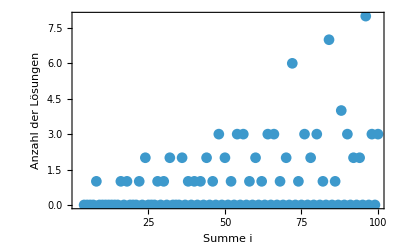

```mathematica
SolutionPerSum={};
For[i=4,i<=100,i++,solutions={};
Do[If[A1+A2+A3+A4==i&&A4^2==A1^2+A2^2+A3^2,AppendTo[solutions,{A1,A2,A3,A4}]],{A1,1,i-3},{A2,A1,i-3},{A3,A2,i-3},{A4,A3,i-3}];
AppendTo[SolutionPerSum,{i,Length[solutions]}]]
ListPlot[SolutionPerSum,PlotRange->All,Frame->True,FrameLabel->{"Sum i","Quantity of Solutions" },PlotMarkers->Automatic]
```

### 6.3 XXX

--- Text here ---

## 7 - Possible Generalizations of the Problem Bezug zu Sensitivity Analysis mit der 18 aufstellen

### 6.1 XXX

--- Text here ---

### 6.2 XXX

--- Text here ---

### 6.3 XXX

--- Text here ---

## 8 Summary of results

--- Text here ---

### 4.3

```mathematica
RecoverEdges[A1_,A2_,A3_]:=Module[{p},p=Sqrt[8*A1*A2*A3];
{p/(2*A3),p/(2*A2),p/(2*A1)}];

RecoverEdges[2,3,6]
```

{√2,2 √2,3 √2}

Each permutation of (A1, A2, A3) from the table in Section 4.2 yields a corresponding permutation of (x, y, z), confirming that the six solutions found represent six geometrically distinct tetrahedra .

Summe = 84

Summe = 86

Summe = 88

Summe = 90

Summe = 92

Summe = 94

Summe = 96

Summe = 98

Summe = 100

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null]